# 1. 齒面誤差繪圖

```mathematica
Off[General::spell1];Off[General::spell];$HistoryLimit=0;
FilePath=NotebookDirectory[];
SetDirectory[FilePath]
```

C:\Users\F1shift\Google Drive\MIRDC\18-24-B-0.08mm+0.2mm\Part v2\2nd\2nd-1st - indent 8, 2, 4, 6

## 1.1 齒面誤差繪圖函式

### 預設圖像解析度與大小設定

```mathematica
CallImageSetting[index_]:=Module[{},
If[index==1,
ImageDPI=600;
cm=72/2.54;(*Mathematica的ImageSize單位是pt，也就是 1/72 in*)
ImageWidth=12*cm;
ImageSizeSetting=ImageSize-> ImageWidth;
ImageResolutionSetting = ImageResolution->ImageDPI;
TextSizePt1=12;
TextSizePt2=9;
FontFamily1=FontFamily-> "Times New Roman";]
If[index==2,
ImageDPI=600;
cm=72/2.54;(*Mathematica的ImageSize單位是pt，也就是 1/72 in*)
ImageWidth=14.65*cm;
ImageSizeSetting=ImageSize-> ImageWidth;
ImageResolutionSetting = ImageResolution->ImageDPI;
TextSizePt1=12;
TextSizePt2=9;
FontFamily1=FontFamily-> "Times New Roman";]
]
```

### Draw Tooth Surface Errors - Gap

#### 線條形式

```mathematica
DrawToothSurfaceErrorsGap[SurfaceDifference_,tsca_]:=Module[{hd,Index,SurfaceErrors,ThickError,ThickErrorI,ThickErrorA,numc,numr,numcm,numrm,theta,thetad,tWidth,tHeight,tw,th,ZeroGridPoints,DevGridPoints,SumSquared,AverageError,ColorSet,LineSet,LineWidth,TextSet,PosiSet,OffsetPosi,di,ans1,ans2,ans3,tr1,FontFormat,ansSurfaceZeroLines,ansSurfaceDevationLines,ansLinkLines,ansAuxiliaryLines,ansErrorValues,ansLables,Output,rowTextUp,rowTextDown,colTextUp,colTextDown},
CallImageSetting[1];
(*Tooth Surface Errors Parameters*)
SurfaceErrors=SurfaceDifference[[1]];
hd=Subscript[h, d]/.SurfaceDifference[[2]];
ThickError=Subscript[Δ, t]/.SurfaceDifference[[2]];
ThickErrorI=Subscript[ΔI, t]/.SurfaceDifference[[2]];
ThickErrorA=Subscript[ΔA, t]/.SurfaceDifference[[2]];
numc=Length[SurfaceErrors[[1]]];
numr=Length[SurfaceErrors[[1]][[1]]];
If[hd<0,Index={2,1};,Index={1,2};];

(*Mean Point Number*)
numcm=Floor[numc/2]+1;
numrm=Floor[numr/2]+1;

(*Plot Parameters*)
theta=35.0Degree;
thetad={45.0,-45.0}Degree;
tHeight=5;
tWidth=tHeight/3*8;
tw=tWidth/(numc-1);
th=tHeight/(numr-1);

(*Grip Positions*)
ZeroGridPoints=Table[{th*ll*Sin[theta]-tw*kk,th*ll*Cos[theta]*(jj*2-1)+(th*2)*jj},{jj,0,1},{kk,0,numc-1},{ll,0,numr-1}];

(*Deviation Positions*)
DevGridPoints=Table[ZeroGridPoints[[jj]][[kk]][[ll]]+tsca*{SurfaceErrors[[Index[[jj]]]][[numc-kk+1]][[ll]]*Cos[thetad[[jj]]],SurfaceErrors[[Index[[jj]]]][[numc-kk+1]][[ll]]*Sin[thetad[[jj]]]},{jj,1,2},{kk,1,numc},{ll,1,numr}];

(*Drawing Zero Grip Lines*)
LineWidth=0.002;
LineSet=Table[ZeroGridPoints[[jj]][[kk]][[ll]],{jj,1,2},{kk,1,numc},{ll,1,numr}];
ans1=Table[Graphics[{Thickness[LineWidth],Gray,Line[LineSet[[jj]][[kk]]]}],{jj,1,2},{kk,1,numc}];
LineSet=Table[ZeroGridPoints[[jj]][[kk]][[ll]],{jj,1,2},{ll,1,numr},{kk,1,numc}];
ans2=Table[Graphics[{Thickness[LineWidth],Gray,Line[LineSet[[jj]][[ll]]]}],{jj,1,2},{ll,1,numr}];
ansSurfaceZeroLines=Join[ans1,ans2];

(*Drawing Deviation Grip Lines*)
LineWidth=0.003;
LineSet=Table[DevGridPoints[[jj]][[kk]][[ll]],{jj,1,2},{kk,1,numc},{ll,1,numr}];
ans1=Table[Graphics[{Blue,Thickness[LineWidth] ,Line[LineSet[[jj]][[kk]]]}],{jj,1,2},{kk,1,numc}];
LineSet=Table[DevGridPoints[[jj]][[kk]][[ll]],{jj,1,2},{ll,1,numr},{kk,1,numc}];
ans2=Table[Graphics[{Blue,Thickness[LineWidth],Line[LineSet[[jj]][[ll]]]}],{jj,1,2},{ll,1,numr}];
ansSurfaceDevationLines=Join[ans1,ans2];

(*Drawing Line Between Deviation and Zero Grip Lines*)
LineWidth=0.003;
ColorSet=Table[If[SurfaceErrors[[Index[[jj]]]][[numc-kk+1]][[ll]]<=0,Green,Red],{jj,1,2},{kk,1,numc},{ll,1,numr}];
LineSet=Table[{ZeroGridPoints[[jj]][[kk]][[ll]],DevGridPoints[[jj]][[kk]][[ll]]},{jj,1,2},{kk,1,numc},{ll,1,numr}];
ansLinkLines=Table[Graphics[{Thickness[LineWidth],ColorSet[[jj]][[kk]][[ll]],Line[LineSet[[jj]][[kk]][[ll]]]}],{jj,1,2},{kk,1,numc},{ll,1,numr}];

(*Other Auxiliary Lines*)
LineSet={{ZeroGridPoints[[1]][[1]][[1]],ZeroGridPoints[[2]][[1]][[1]]},{ZeroGridPoints[[1]][[numc]][[1]],ZeroGridPoints[[2]][[numc]][[1]]}};
ansAuxiliaryLines=Table[Graphics[{Thickness[0.002],Gray,Line[LineSet[[kk]]]}],{kk,1,Length[LineSet]}];

(*Lable*)
di={-1,1};
rowTextUp=Table[Graphics[{Text[Style[ll,TextSizePt2,FontFamily1],ZeroGridPoints[[2]][[1]][[ll]]+{0.7,0}]}],{ll,1,numr}];
rowTextDown=Table[Graphics[{Text[Style[ll,TextSizePt2,FontFamily1],ZeroGridPoints[[1]][[1]][[ll]]+{0.7,0}]}],{ll,1,numr}];
colTextUp=Table[Graphics[{Text[Style[FromCharacterCode[64+kk],TextSizePt2,FontFamily1],Last[ZeroGridPoints[[2]][[numc+1-kk]]]+di[[2]]*{0,0.8}+{0.5,0}]}],{kk,1,numc}];
colTextDown=Table[Graphics[{Text[Style[FromCharacterCode[64+kk],TextSizePt2,FontFamily1],Last[ZeroGridPoints[[1]][[numc+1-kk]]]+di[[1]]*{0,0.8}+{0.5,0}]}],{kk,1,numc}];
If[hd<0,TextSet={"Root","Tip","Tip","Back","Front","Gap"};,
TextSet={"Root","Tip","Tip","Back","Front","Gap"};];
PosiSet={(ZeroGridPoints[[1]][[1]][[1]]+ZeroGridPoints[[2]][[numc]][[1]])/2,(ZeroGridPoints[[1]][[1]][[numr]]+ZeroGridPoints[[1]][[numc]][[numr]])/2-{0,1.6},(ZeroGridPoints[[2]][[1]][[numr]]+ZeroGridPoints[[2]][[numc]][[numr]])/2+{0,1.8},(ZeroGridPoints[[1]][[1]][[1]]+ZeroGridPoints[[2]][[1]][[1]])/2-{1.0,0},(ZeroGridPoints[[1]][[numc]][[1]]+ZeroGridPoints[[2]][[numc]][[1]])/2+{0.9,0},(ZeroGridPoints[[1]][[1]][[1]]+ZeroGridPoints[[2]][[1]][[1]])/2+{3.5,0}};
FontFormat=Join[Table[{TextSizePt1,FontFamily1,FontWeight->Bold,FontSlant->Italic},{ii,1,Length[TextSet]}],{{TextSizePt2,FontFamily1,FontWeight->Bold,FontSlant->Plain}}];
ans3=Table[Graphics[{Text[Style[TextSet[[ii]],FontFormat[[ii]][[1]],FontFormat[[ii]][[2]],FontFormat[[ii]][[3]]],PosiSet[[ii]]]}],{ii,1,Length[TextSet]}];
ansLables=Join[rowTextUp,rowTextDown,colTextUp,colTextDown ,ans3];

(*Output Error Values*)
TextSet=Table[SurfaceErrors[[Index[[jj]]]][[(numc-1)*(2-kk)+1]][[(numr-1)*(ll-1)+1]],{jj,1,2},{kk,1,2},{ll,1,2}];
ColorSet=Table[If[TextSet[[jj]][[kk]][[ll]]<=0,Darker[Green],Darker[Red]],{jj,1,2},{kk,1,2},{ll,1,2}];
OffsetPosi={{1.7,0},{-1.4,0}};
PosiSet=Table[ZeroGridPoints[[jj]][[(numc-1)*(kk-1)+1]][[(numr-1)*(ll-1)+1]]+OffsetPosi[[kk]],{jj,1,2},{kk,1,2},{ll,1,2}];
ans1=Table[Graphics[{Gray,Text[Style[Round[TextSet[[jj]][[kk]][[ll]]*1000,0.1],ColorSet[[jj]][[kk]][[ll]],TextSizePt2,FontFamily1],PosiSet[[jj]][[kk]][[ll]]]}],{jj,1,2},{kk,1,2},{ll,1,2}];
SumSquared=∑_(jj=1)^2 ∑_(kk=1)^numc ∑_(ll=1)^numr (SurfaceErrors[[jj]][[kk]][[ll]]*1000)^2;
AverageError=∑_(jj=1)^2 ∑_(kk=1)^numc ∑_(ll=1)^numr (Abs[SurfaceErrors[[jj]][[kk]][[ll]]]*1000)/(2*numc*numr);
TextSet="Average Error: "<>ToString[NumberForm[Round[AverageError,1],DigitBlock->3]]<>" μm     "<>"Sum of Squared: "<>ToString[NumberForm[Round[SumSquared,1],DigitBlock->3]]<>" μm^2"<>"\nSpace Error: "<>ToString[Round[ThickError*1000,0.01]]<>" μm"<>", Cutter I: "<>ToString[Round[ThickErrorI*1000,0.01]]<>" μm"<>", Cutter A: "<>ToString[Round[ThickErrorA*1000,0.01]]<>" μm"<>", Sum: "<>ToString[Round[(ThickErrorI+ThickErrorA)*1000,0.01]]<>" μm";
tr1=(ZeroGridPoints[[1]][[1]][[numr]]+ZeroGridPoints[[1]][[numc]][[numr]])/2;
PosiSet=tr1-{0,2.8};
ans2={Graphics[{Text[Style[TextSet,TextSizePt2,FontFamily1],PosiSet]}]};
ansErrorValues=Join[ans1,ans2];

(*Return Picture*)
Output={ansSurfaceZeroLines,ansSurfaceDevationLines,ansLinkLines,ansAuxiliaryLines,ansLables,ansErrorValues};

(*Output={ansSurfaceZeroLines,ansSurfaceDevationLines,ansLinkLines,ansAuxiliaryLines};*)
Return[Output];
];
```

#### 數字形式

```mathematica
DrawToothSurfaceErrorsGapNum[SurfaceDifference_,tsca_]:=Module[{},
CallImageSetting[2];
SurfaceErrors=SurfaceDifference[[1]]*1000;
hd=Subscript[h, d]/.SurfaceDifference[[2]];
ThickError=(Subscript[Δ, t]/.SurfaceDifference[[2]])*1000;
ThickErrorI=(Subscript[ΔI, t]/.SurfaceDifference[[2]])*1000;
ThickErrorA=(Subscript[ΔA, t]/.SurfaceDifference[[2]])*1000;
NRow=Dimensions[SurfaceErrors][[3]];
NCol=Dimensions[SurfaceErrors][[2]];
(*Set Box Parameter*)
numc=Length[SurfaceErrors[[1]]];
numr=Length[SurfaceErrors[[1]][[1]]];
theta=60Degree;
thetad=90.0Degree;
tWidth=65.0;
tHeight=20.0;
h1=5;
h2=h1+2*tHeight;
(*Plot Box*)
ans1=Graphics[{Gray,Line[{{0,h1/2},{0,-h1/2}}]}];
ans2=Graphics[{Gray,Line[{{tWidth,h1/2},{tWidth,-h1/2}}]}];
ans3=Graphics[{Gray,Line[{{0,h1/2},{tWidth,h1/2}}]}];
ans4=Graphics[{Gray,Line[{{0,-h1/2},{tWidth,-h1/2}}]}];
ans5=Graphics[{Gray,Line[{{0,h1/2},{tHeight*Cos[theta],h2/2}}]}];
ans6=Graphics[{Gray,Line[{{tWidth,h1/2},{tWidth+tHeight*Cos[theta],h2/2}}]}];
ans7=Graphics[{Gray,Line[{{tHeight*Cos[theta],h2/2},{tWidth+tHeight*Cos[theta],h2/2}}]}];
ans8=Graphics[{Gray,Line[{{0,-h1/2},{tHeight*Cos[theta],-h2/2}}]}];
ans9=Graphics[{Gray,Line[{{tWidth,-h1/2},{tWidth+tHeight*Cos[theta],-h2/2}}]}];
ans10=Graphics[{Gray,Line[{{tHeight*Cos[theta],-h2/2},{tWidth+tHeight*Cos[theta],-h2/2}}]}];
(*建立數值點配對位置*)
Concavelocation=Table[{tWidth/NCol*(jj-0.5)+tHeight*Cos[theta]/NRow*(ii-0.5),-(h1/2.0+tHeight/(NRow)*(ii-0.5))},{jj,1,NCol},{ii,1,NRow}];
Convexlocation=Table[{tWidth/NCol*(jj-0.5)+tHeight*Cos[theta]/NRow*(ii-0.5),(h1/2.0+tHeight/(NRow)*(ii-0.5))},{jj,1,NCol},{ii,1,NRow}];
(*凸面數值配對&顏色區分*)
numFontSize=(tHeight/NRow)/25.4*72;
numberconvex=Table[Graphics[Text[Style[SurfaceErrors[[1]][[kk]][[ll]],numFontSize,If[SurfaceErrors[[1]][[kk]][[ll]]<=0,Green,Red]],Convexlocation[[kk]][[ll]]]],{ll,1,NRow},{kk,1,NCol}];
(*凹面數值配對&顏色區分*)
numberconcave=Table[Graphics[Text[Style[SurfaceErrors[[2]][[kk]][[ll]],numFontSize,If[SurfaceErrors[[2]][[kk]][[ll]]<=0,Green,Red]],Concavelocation[[kk]][[ll]]]],{ll,1,NRow},{kk,1,NCol}];
(*A~M上下兩排字母*)
ABCposition1=Table[{tHeight*Cos[theta]+tWidth/NCol*(ii+0.5),(h2/2 + TextSizePt2/72*25.4)},{ii,0,NCol-1}];
ABCposition2=Table[{tHeight*Cos[theta]+tWidth/NCol*(ii+0.5),-(h2/2 + TextSizePt2/72*25.4)},{ii,0,NCol-1}];
nameABC=Table[FromCharacterCode[i],{i,65,90}];
OnABC=Table[Graphics[Text[Style[nameABC[[ii]],TextSizePt2],ABCposition1[[ii]]]],{ii,1,NCol}];
OffABC=Table[Graphics[Text[Style[nameABC[[ii]],TextSizePt2],ABCposition2[[ii]]]],{ii,1,NCol}];
(*1~10上下兩排數字*)
Numberposition1=Table[{tWidth+TextSizePt2/72*25.4+tHeight*Cos[theta]/NRow * (jj-1+0.5),tHeight/(NRow)*(jj-0.5)+h1/2},{jj,1,NRow}];
Numnerposition2=Table[{tWidth+TextSizePt2/72*25.4+tHeight*Cos[theta]/NRow * (jj-1+0.5),-(tHeight/(NRow)*(jj-0.5)+h1/2)},{jj,1,NRow}];
number=Table[i,{i,1,NRow}];
OnNumber=Table[Graphics[Text[Style[number[[jj]],TextSizePt2],Numberposition1[[jj]]]],{jj,1,NRow}];
OffNumber=Table[Graphics[Text[Style[number[[jj]],TextSizePt2],Numnerposition2[[jj]]]],{jj,1,NRow}];

(*Label*)
ToePosition={-3.5,0};
ToplandPosition={tWidth/2,0};
HeelPosition={tWidth+3.5,0};
OnRootPosition={76,40};
OffRootPosition={76,-40};
LaToe=Graphics[Text[Style[ToString["Front"],TextSizePt1,FontWeight->Bold],{TextSizePt1 /72*25.4*1.5, 0}]];
LaRoot=Graphics[Text[Style[ToString["Root"],TextSizePt1,FontWeight->Bold],{tWidth/2,0}]];
LaHeel=Graphics[Text[Style[ToString["Back"],TextSizePt1,FontWeight->Bold],{tWidth-TextSizePt1 /72*25.4*1.5,0}]];
LaTip1=Graphics[Text[Style[ToString["Tip"],TextSizePt1,FontWeight->Bold],{tWidth/2+tHeight*Cos[theta]*0.5,h2/2+TextSizePt1/72*25.4*1.5}]];
LaTip2=Graphics[Text[Style[ToString["Tip"],TextSizePt1,FontWeight->Bold],{tWidth/2+tHeight*Cos[theta]*0.5,-(h2/2+TextSizePt1/72*25.4*1.5)}]];

(*Output Error Values*)
TextSet=Table[SurfaceErrors[[jj]][[(numc-1)*(2-kk)+1]][[(numr-1)*(ll-1)+1]],{jj,1,2},{kk,1,2},{ll,1,2}];
ColorSet=Table[If[TextSet[[jj]][[kk]][[ll]]<=0,Darker[Green],Darker[Red]],{jj,1,2},{kk,1,2},{ll,1,2}];
OffsetPosi={{1.7,0},{-1.4,0}};
PosiSet=Table[SurfaceErrors[[jj]][[(numc-1)*(kk-1)+1]][[(numr-1)*(ll-1)+1]]+OffsetPosi[[kk]],{jj,1,2},{kk,1,2},{ll,1,2}];

SumSquared=∑_(jj=1)^2 ∑_(kk=1)^numc ∑_(ll=1)^numr (SurfaceErrors[[jj]][[kk]][[ll]])^2;
AverageError=∑_(jj=1)^2 ∑_(kk=1)^numc ∑_(ll=1)^numr (Abs[SurfaceErrors[[jj]][[kk]][[ll]]])/(2*numc*numr);
TextSet="Average Error: "<>ToString[NumberForm[Round[AverageError,1],DigitBlock->3]]<>" μm     "<>"Sum of Squared: "<>ToString[NumberForm[Round[SumSquared,1],DigitBlock->3]]<>" μm^2"<>"\nSpace Error: "<>ToString[Round[ThickError,0.01]]<>" μm"<>", Cutter I: "<>ToString[Round[ThickErrorI,0.01]]<>" μm"<>", Cutter A: "<>ToString[Round[ThickErrorA,0.01]]<>" μm"<>", Sum: "<>ToString[Round[(ThickErrorI+ThickErrorA),0.01]]<>" μm";
ans11={Graphics[{Text[Style[TextSet,TextSizePt2,FontFamily1],{(tWidth+tHeight*Cos[theta]*1.5)/2, -h2/2-(TextSizePt1+TextSizePt2)/72*25.1*1.5}]}]};
Return[{ans1,ans2,ans3,ans4,ans5,ans6,ans7,ans8,ans9,ans10,ans11,numberconvex,numberconcave,OnABC,OffABC,OnNumber,OffNumber,LaToe,LaRoot,LaHeel,LaTip1,LaTip2}];
]
```

## 1.2 總齒面誤差

```mathematica
scale=5;
```

### 平均誤差

{h_d→-1,Δ_t→-0.00683734,ΔI_t→0.0330738,ΔA_t→0.0399111,α_s→{0.154502,0.154502}}

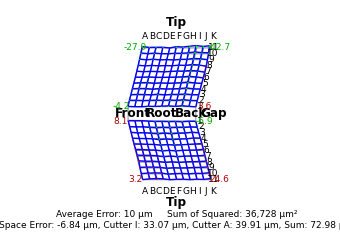

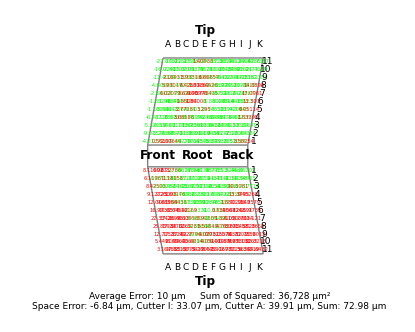

平均齒面誤差1-圖形.png

平均齒面誤差1-數據.png

```mathematica
PitchError=Import["PitchError_Average.json"];
Error=Import["FaceError_Average.json"];
setting={Subscript[h, d]->-1,Subscript[Δ, t]->PitchError[[1]]-PitchError[[2]],Subscript[ΔI, t]->PitchError[[1]],Subscript[ΔA, t]->PitchError[[2]],Subscript[α, s]->{0.1545021283066487,0.15450212830917667}}
Error={Transpose[Error[[1]]], Transpose[Error[[2]]]};
ErrorAndSetting = {
Error,
setting
};
la=Show[DrawToothSurfaceErrorsGap[ErrorAndSetting, scale],ImageSizeSetting]
laNum=Show[DrawToothSurfaceErrorsGapNum[ErrorAndSetting, scale],ImageSizeSetting]
Export["平均齒面誤差1-圖形.png",la,ImageResolutionSetting]
Export["平均齒面誤差1-數據.png",laNum,ImageResolutionSetting]
```

### 各齒誤差-量測部分

```mathematica
EachPitchError=Import["PitchError_EachTooth.json"];
EachError=Import["FaceError_EachTooth.json"];
```

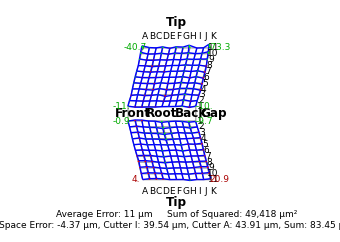

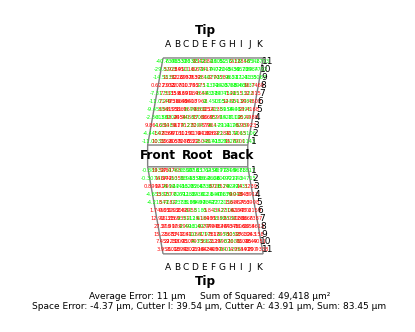

齒面誤差1-1-圖形.png

齒面誤差1-1-數據.png

```mathematica
ti=1;
PitchError=EachPitchError[[ti]];
setting={Subscript[h, d]->-1,Subscript[Δ, t]->PitchError[[1]]-PitchError[[2]],Subscript[ΔI, t]->PitchError[[1]],Subscript[ΔA, t]->PitchError[[2]],Subscript[α, s]->{0.1545021283066487,0.15450212830917667}};
Error={Transpose[EachError[[ti]][[1]]], Transpose[EachError[[ti]][[2]]]};
ErrorAndSetting = {
Error,
setting
};
la=Show[DrawToothSurfaceErrorsGap[ErrorAndSetting, scale],ImageSizeSetting]
laNum=Show[DrawToothSurfaceErrorsGapNum[ErrorAndSetting, scale],ImageSizeSetting]
Export["齒面誤差1-"<>ToString[ti]<>"-圖形.png",la,ImageResolutionSetting]
Export["齒面誤差1-"<>ToString[ti]<>"-數據.png",laNum,ImageResolutionSetting]
```

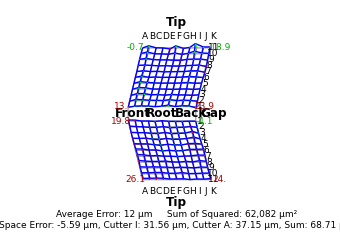

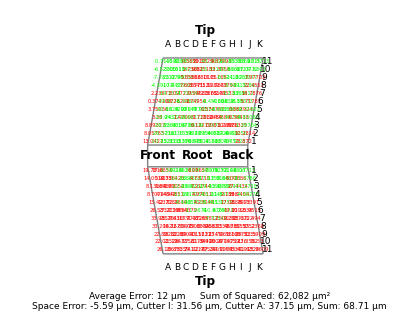

齒面誤差1-2-圖形.png

齒面誤差1-2-數據.png

```mathematica
ti=2;
PitchError=EachPitchError[[ti]];
setting={Subscript[h, d]->-1,Subscript[Δ, t]->PitchError[[1]]-PitchError[[2]],Subscript[ΔI, t]->PitchError[[1]],Subscript[ΔA, t]->PitchError[[2]],Subscript[α, s]->{0.1545021283066487,0.15450212830917667}};
Error={Transpose[EachError[[ti]][[1]]], Transpose[EachError[[ti]][[2]]]};
ErrorAndSetting = {
Error,
setting
};
la=Show[DrawToothSurfaceErrorsGap[ErrorAndSetting, scale],ImageSizeSetting]
laNum=Show[DrawToothSurfaceErrorsGapNum[ErrorAndSetting, scale],ImageSizeSetting]
Export["齒面誤差1-"<>ToString[ti]<>"-圖形.png",la,ImageResolutionSetting]
Export["齒面誤差1-"<>ToString[ti]<>"-數據.png",laNum,ImageResolutionSetting]
```

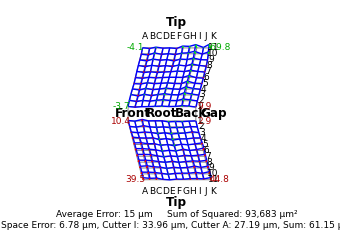

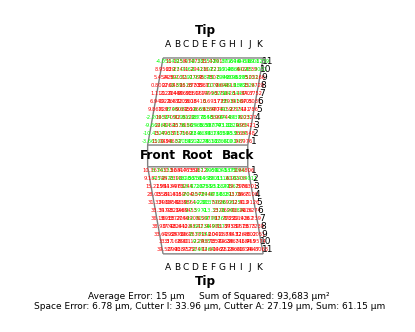

齒面誤差1-3-圖形.png

齒面誤差1-3-數據.png

```mathematica
ti=3;
PitchError=EachPitchError[[ti]];
setting={Subscript[h, d]->-1,Subscript[Δ, t]->PitchError[[1]]-PitchError[[2]],Subscript[ΔI, t]->PitchError[[1]],Subscript[ΔA, t]->PitchError[[2]],Subscript[α, s]->{0.1545021283066487,0.15450212830917667}};
Error={Transpose[EachError[[ti]][[1]]], Transpose[EachError[[ti]][[2]]]};
ErrorAndSetting = {
Error,
setting
};
la=Show[DrawToothSurfaceErrorsGap[ErrorAndSetting, scale],ImageSizeSetting]
laNum=Show[DrawToothSurfaceErrorsGapNum[ErrorAndSetting, scale],ImageSizeSetting]
Export["齒面誤差1-"<>ToString[ti]<>"-圖形.png",la,ImageResolutionSetting]
Export["齒面誤差1-"<>ToString[ti]<>"-數據.png",laNum,ImageResolutionSetting]
```

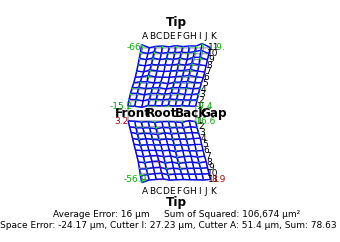

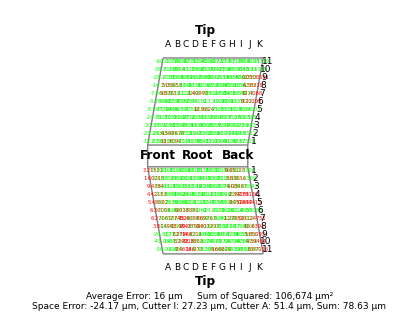

齒面誤差1-4-圖形.png

齒面誤差1-4-數據.png

```mathematica
ti=4;
PitchError=EachPitchError[[ti]];
setting={Subscript[h, d]->-1,Subscript[Δ, t]->PitchError[[1]]-PitchError[[2]],Subscript[ΔI, t]->PitchError[[1]],Subscript[ΔA, t]->PitchError[[2]],Subscript[α, s]->{0.1545021283066487,0.15450212830917667}};
Error={Transpose[EachError[[ti]][[1]]], Transpose[EachError[[ti]][[2]]]};
ErrorAndSetting = {
Error,
setting
};
la=Show[DrawToothSurfaceErrorsGap[ErrorAndSetting, scale],ImageSizeSetting]
laNum=Show[DrawToothSurfaceErrorsGapNum[ErrorAndSetting, scale],ImageSizeSetting]
Export["齒面誤差1-"<>ToString[ti]<>"-圖形.png",la,ImageResolutionSetting]
Export["齒面誤差1-"<>ToString[ti]<>"-數據.png",laNum,ImageResolutionSetting]
```

## 1.3 補償齒面與補償目標差距

```mathematica
scale=5;
```

### 補償目標

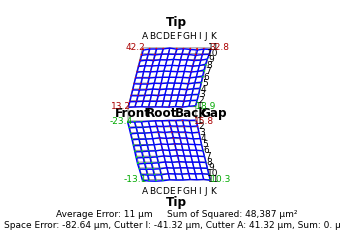

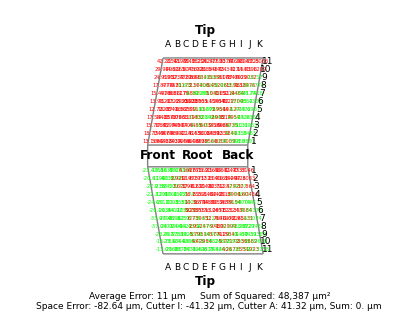

原始齒型與補償目標差距1-圖形.png

原始齒型與補償目標差距1-數據.png

```mathematica
PitchError=Import["ModifyTargetPitchError1.json"];
Error=Import["ModifyTargetFaceError1.json"];
setting={Subscript[h, d]->-1,Subscript[Δ, t]->PitchError[[1]]-PitchError[[2]],Subscript[ΔI, t]->PitchError[[1]],Subscript[ΔA, t]->PitchError[[2]],Subscript[α, s]->{0.1545021283066487,0.15450212830917667}};
Error={Transpose[Error[[1]]], Transpose[Error[[2]]]};
ErrorAndSetting = {
Error,
setting
};
la=Show[DrawToothSurfaceErrorsGap[ErrorAndSetting, scale],ImageSizeSetting]
laNum=Show[DrawToothSurfaceErrorsGapNum[ErrorAndSetting, scale],ImageSizeSetting]
Export["補償目標1-圖形.png",la,ImageResolutionSetting];
Export["補償目標1-數據.png",laNum,ImageResolutionSetting];
```

### 補償量

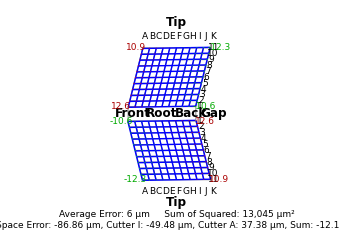

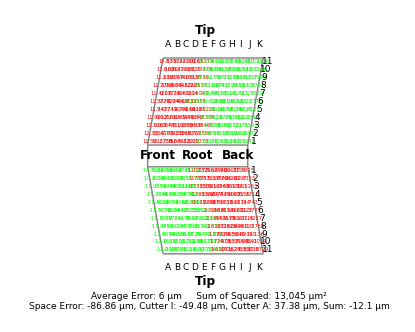

原始齒型與補償目標差距1-圖形.png

原始齒型與補償目標差距1-數據.png

```mathematica
PitchError=Import["ModiyedPitchError1.json"];
Error=Import["ModiyedFaceError1.json"];
setting={Subscript[h, d]->-1,Subscript[Δ, t]->PitchError[[1]]-PitchError[[2]],Subscript[ΔI, t]->PitchError[[1]],Subscript[ΔA, t]->PitchError[[2]],Subscript[α, s]->{0.1545021283066487,0.15450212830917667}};
Error={Transpose[Error[[1]]], Transpose[Error[[2]]]};
ErrorAndSetting = {
Error,
setting
};
la=Show[DrawToothSurfaceErrorsGap[ErrorAndSetting, scale],ImageSizeSetting]
laNum=Show[DrawToothSurfaceErrorsGapNum[ErrorAndSetting, scale],ImageSizeSetting]
Export["補償量1-圖形.png",la,ImageResolutionSetting];
Export["補償量1-數據.png",laNum,ImageResolutionSetting];
```

### 殘餘補償量

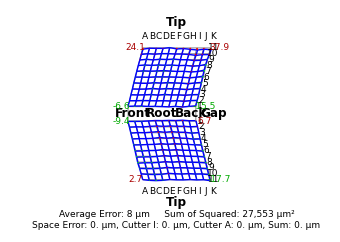

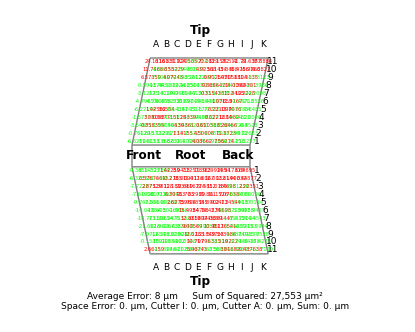

補償齒型與補償目標差距1-圖形.png

補償齒型與補償目標差距1-數據.png

```mathematica
setting={Subscript[h, d]->-1,Subscript[Δ, t]->0,Subscript[ΔI, t]->0,Subscript[ΔA, t]->0,Subscript[α, s]->{0.1545021283066487,0.15450212830917667}};
Error=Import["ResidualDistances1.json"];
Error={Transpose[Error[[1]]], Transpose[Error[[2]]]};
ErrorAndSetting = {
Error,
setting
};
la=Show[DrawToothSurfaceErrorsGap[ErrorAndSetting, scale],ImageSizeSetting]
laNum=Show[DrawToothSurfaceErrorsGapNum[ErrorAndSetting, scale],ImageSizeSetting]
Export["殘餘補償量1-圖形.png",la,ImageResolutionSetting];
Export["殘餘補償量1-數據.png",laNum,ImageResolutionSetting];
```